```mathematica
Vs={0.00550983,-0.22853265,-0.15235455,-0.33863702 ,0.35037867,0.06018662,-0.0860958,-0.04642701 ,0.05930989,0.16991714}
```

{0.00550983,-0.228533,-0.152355,-0.338637,0.350379,0.0601866,-0.0860958,-0.046427,0.0593099,0.169917}

```mathematica
xs = Table[xi,{xi,-0.5,0.5, 1/9}];
```

```mathematica
pot = Transpose[{xs,Vs}];
```

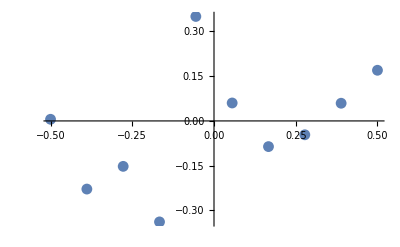

```mathematica
plt1=ListPlot[pot]
```

```mathematica
a0=-0.071817594629629569;
```

```mathematica
ans={0.06117713,0.16776262,0.08130395,0.08372183,-0.08372183,-0.08130395,-0.16776262,-0.06117713,0.07181759,-0.06117713};
```

```mathematica
bns = {9.42697632*10^(-02),-6.91435830*10^(-02),-1.62216511*10^(-02),-1.20678561*10^(-01),-1.20678561*10^(-01),-1.62216511*10^(-02),-6.91435830*10^(-02),9.42697632*10^(-02),-1.66706002*10^(-17),-9.42697632*10^(-02)};
```

```mathematica
V[x_]:=1/2*a0 + Sum[ans[[n]]*Cos[2*n*Pi*x]+bns[[n]]*Sin[2*n*Pi*x],{n,1,10}]
```

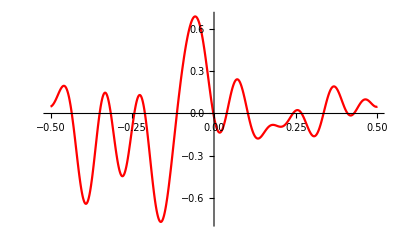

```mathematica
plt2=Plot[V[x],{x,-1/2,1/2},PlotStyle->Red]
```

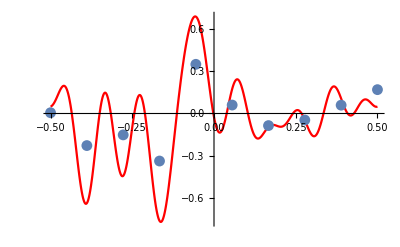

```mathematica
Show[plt2,plt1]
```